```mathematica
nf12[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1}];
ng12[y_,t_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1}];
inf12[y_,t_]:=NIntegrate[nf12[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing12[y_,t_]:=NIntegrate[ng12[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
nf13[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1}];
ng13[y_,t_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1}];
inf13[y_,t_]:=NIntegrate[nf13[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing13[y_,t_]:=NIntegrate[ng13[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
nf14[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1}];
ng14[y_,t_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1}];
inf14[y_,t_]:=NIntegrate[nf14[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing14[y_,t_]:=NIntegrate[ng14[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
lf2=ParallelTable[{{y,t},inf12[y,t]},{y,-0.01,0.01,0.001},{t,Join[Range[-1,-0.1,0.05],Range[-0.05,-0.03562509090909091,0.005]]}];

lf3=ParallelTable[{{y,t},inf13[y,t]},{y,-0.001,0.001,0.0001},{t,Join[Range[-1,-0.1,0.05],Range[-0.05,-0.03562509090909091,0.005]]}];

lf4=ParallelTable[{{y,t},inf14[y,t]},{y,-0.0001,0.0001,0.00001},{t,Join[Range[-1,-0.1,0.05],Range[-0.05,-0.03562509090909091,0.005]]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
inf14[-0.00005,-1]
```

-15135.963 ⅈ

```mathematica
Integrate[DiracDelta[y+0.1],{y,-0.1,1}]
```

HeavisideTheta[0.]

```mathematica
HeavisideTheta[0.]
```

HeavisideTheta[0.]

```mathematica
NIntegrate[ng14[y,-1],{y,-0.0001,0.0001},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.73340862671015481126188934021358571619498255964946187892168×10^-14 ⅈ and 7.07214900304798982497063618865776408492736316672779308597514×10^-16 for the integral and error estimates.

-2.733408627×10^-14 ⅈ

```mathematica
NIntegrate[ng13[y,-1],{y,-0.001,0.001},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-12.42192673 ⅈ

```mathematica
NIntegrate[ng12[y,-1],{y,-0.01,0.01},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-12.42626587 ⅈ

```mathematica
NIntegrate[ng1[y,-1],{y,-0.1,0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
NIntegrate[nf1[y,-1],{y,-0.1,0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.522053492 ⅈ

```mathematica
NIntegrate[nf12[y,-1],{y,-0.01,0.01},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.522055965 ⅈ

```mathematica
NIntegrate[nf13[y,-1],{y,-0.001,0.001},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.522055989 ⅈ

```mathematica
NIntegrate[nf14[y,-1],{y,-0.0001,0.0001},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.52205599 ⅈ

```mathematica
nf1x2[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];
ng1x2[y_,t_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];nf1x3[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.3,Λ->L1}];
ng1x3[y_,t_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.3,Λ->L1}];nf1x4[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.4,Λ->L1}];
ng1x4[y_,t_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.4,Λ->L1}];
```

```mathematica
NIntegrate[nf1x2[y,-1],{y,-0.2,0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.522045999 ⅈ

```mathematica
NIntegrate[nf1x3[y,-1],{y,-0.3,0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.522043194 ⅈ

```mathematica
NIntegrate[nf1x4[y,-1],{y,-0.4,0.4},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.522207488 ⅈ

```mathematica
inf2[-1]
```

0.+5.2702 ⅈ

```mathematica
f2
```

(k3 ((64 ⅈ MB^2 P1^2 π (1-x)^3 (mm^2-Λ^2)^4 ξ^2)/((k3^2+mm^2 x+(1-x) Λ^2)^4)+(4 ⅈ π Q^2 (1-x)^3 (mm^2-Λ^2)^4 (-4 P1^2+4 P1^2 ξ^2))/((k3^2+mm^2 x+(1-x) Λ^2)^4)))/(8 P1^2 (4 MB^2 ξ^2+Q^2 (-1+ξ^2)))

```mathematica
Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,Λ->L1}]
```

-((0.+5.8174 ⅈ) k3 (-1.+x)^3)/((1.+k3^2-0.980928 x)^4)

```mathematica
ng2[-1]
```

0.+0. ⅈ

```mathematica
nf2[-1]
```

((0.+6.0323 ⅈ) k3 ((-1.+0. ⅈ) ((-1.+0. ⅈ)+(1.+0. ⅈ) x)^3+(0.0356251+0. ⅈ) ((-1.+0. ⅈ)+(1.+0. ⅈ) x)^3))/(1.+k3^2-0.980928 x)^4

```mathematica
ng1[0.05,-1]
```

-((409.147 k3 ((0.-0.000146669 ⅈ)-(0.+0.000095494 ⅈ) k3^2-(0.+7.83219×10^-18 ⅈ) k3^4+0.977103 k3 ((0.-0.000348072 ⅈ)-(0.+0.000133362 ⅈ) k3^2) Cos[θ]-(0.+0.000190988 ⅈ) k3^2 Cos[θ]^2))/((1.4793+1. k3^2+1.46566 k3 Cos[θ])^2 (1.72454+1. k3^2+1.46566 k3 Cos[θ])^4))

```mathematica
Simplify[%56]
```

(k3 ((0.+0.0600091 ⅈ)+(0.+0.0781421 ⅈ) k3^2+(0.+3.20451×10^-15 ⅈ) k3^4+((0.+0.139152 ⅈ) k3+(0.+0.0533155 ⅈ) k3^3) Cos[θ]+(0.+0.039071 ⅈ) k3^2 Cos[2 θ]))/((1.4793+1. k3^2+1.46566 k3 Cos[θ])^2 (1.72454+1. k3^2+1.46566 k3 Cos[θ])^4)

```mathematica
ing1[0.05,-1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.00003973496571 ⅈ

```mathematica
inf1[0.05,-1]
```

1.428701191 ⅈ

```mathematica
ing1[-0.05,-1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.005300841505 ⅈ

```mathematica
lg11=ParallelTable[{y,I*ing1[y,-1]},{y,-0.1,0.1,0.01}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
sg11=Interpolation[lg11];
```

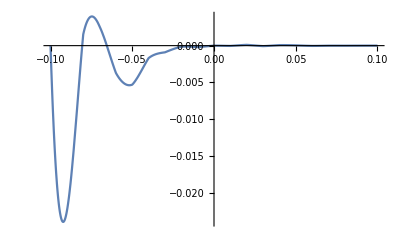

```mathematica
Plot[I*sg11[y],{y,-0.1,0.1},PlotRange->All]
```

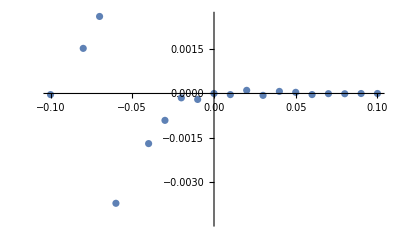

```mathematica
ListPlot[lg11]
```

```mathematica
ing1x2[y_,t_]:=NIntegrate[ng1x2[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing1x3[y_,t_]:=NIntegrate[ng1x3[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing1x4[y_,t_]:=NIntegrate[ng1x4[y,t],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
lg12=ParallelTable[{y,I*ing1x2[y,-1]},{y,-0.2,0.2,0.01}];
lg13=ParallelTable[{y,I*ing1x3[y,-1]},{y,-0.3,0.3,0.01}];
lg14=ParallelTable[{y,I*ing1x4[y,-1]},{y,-0.4,0.4,0.01}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.880937503×10^-16 ⅈ and 1.15381579×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.91913474143433791544750021488596988460676226428367585493176×10^-16 ⅈ and 1.90118919511608785511686734107538920634866268011376479100015×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.87510272997493843751721211918634669636315762166430062051158×10^-15 ⅈ and 2.69277286033283447023707929925670676965136534746123751533898×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.59430565701770185504718083355522938658297876438154619753306×10^-16 ⅈ and 2.24581564267730440026269563016004297086972230977739515438344×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.47691500226713204552413175410529157176679506572562774885966×10^-16 ⅈ and 4.27443301863337740844977137473570976823895850815067571137288×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00126422966558828441161539953900417066431353814797864538404×10^-16 ⅈ and 6.09736248128821477399721282186383573308622363153272094608558×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.74241086616955777629138010647218985692673447940410608366237×10^-16 ⅈ and 3.89476414769657865382354073519612201872852301986812302129442×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.10213235333289954296059588516318332153694862488150994122281×10^-16 ⅈ and 3.61034552801415852479149060442275788777058909601608268369775×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.68376843884814949882771492195293667421089636557926733383207×10^-15 ⅈ and 1.65676928369368780386465409465705230974445684516780538191877×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.87666025430809414031674225397747220932262544480594455845304×10^-15 ⅈ and 4.33692185341797797914170160348214382914866267647890230835513×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.13996487889585497118113921715297287587583587798692333405504×10^-14 ⅈ and 7.82254244165812570971135505600014225591226554442993434025976×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.14250926427487659372252623815588301067141820675195756021465×10^-15 ⅈ and 2.88442115056496025623467601180997688049279789998354051318121×10^-16 for the integral and error estimates.

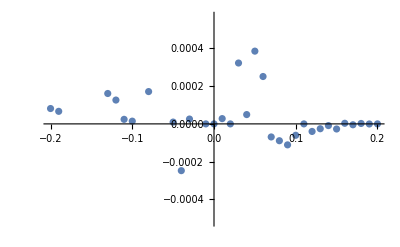

```mathematica
ListPlot[lg12]
```

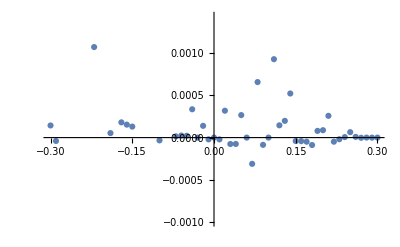

```mathematica
ListPlot[lg13]
```

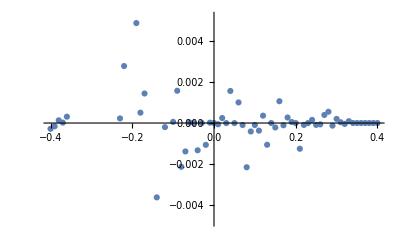

```mathematica
ListPlot[lg14]
```

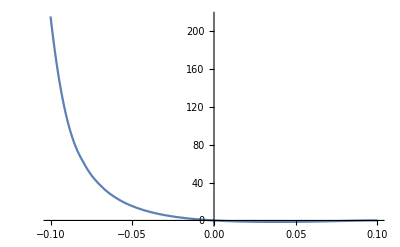

```mathematica
Plot[I*sf1[y,-1],{y,-0.1,0.1},PlotRange->All]
```

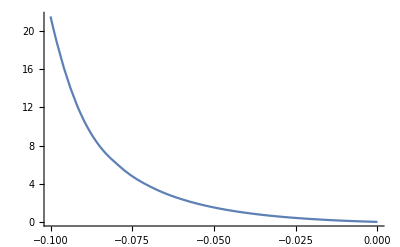

```mathematica
Plot[I*0.1*sf1[y,-1],{y,-0.1,0},PlotRange->All]
```

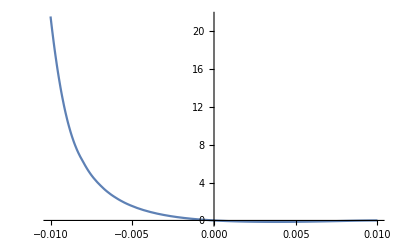

```mathematica
Plot[I*0.01*sf2[y,-1],{y,-0.01,0.01},PlotRange->All]
```

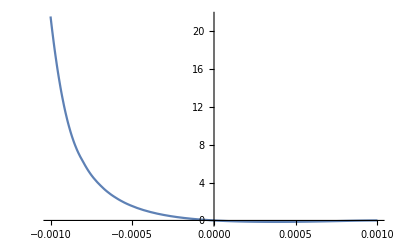

```mathematica
Plot[I*0.001*sf3[y,-1],{y,-0.001,0.001},PlotRange->All]
```

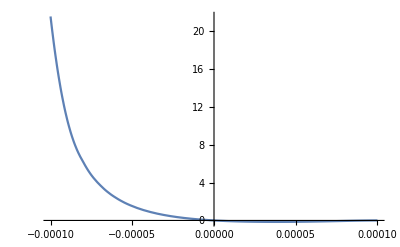

```mathematica
Plot[I*0.0001*sf4[y,-1],{y,-0.0001,0.0001},PlotRange->All]
```

```mathematica
NIntegrate[(1/y)*nf1x2[y,-1],{y,-0.2,0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

26.34953628 ⅈ

```mathematica
NIntegrate[nf1x2[y,-1],{y,-0.2,0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.522045999 ⅈ

```mathematica
NIntegrate[(1/y)*ng1[y,-1],{y,-0.1,0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.22628900952020091146717308139429070522439235458420080483845×10^-12 ⅈ and 1.06435366548016959870756163034103636243257883687891980694052×10^-8 for the integral and error estimates.

7.22628901×10^-12 ⅈ

```mathematica
NIntegrate[ng1[0.05,-1],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5.680707556×10^-15 ⅈ